To run the code, connect to the NDrive. Then evaluate the ‘Setup’, ‘Load’ and ‘Functions’ sections.

### Setup

#### Default options for plots, error messages, and colors

```mathematica
SetDirectory["/Volumes/ni_lab/NaCs1pt5/NaCsSimulationPrecomputedMatrices/groundStateHamiltonian"];
SetOptions[Plot,BaseStyle->{FontFamily->"Arial",FontSize->20},TicksStyle->Directive[Black,10],Frame->True,FrameTicks->{Automatic,Automatic},ImageSize->500,AxesLabel->{"",""},PlotStyle->Black]; 
SetOptions[ListPlot,BaseStyle->{FontFamily->"Arial",FontSize->20},TicksStyle->Directive[Black,10],Frame->True,FrameTicks->{Automatic,Automatic},ImageSize->500,AxesLabel->{"",""}]; 
ParallelEvaluate[Off[ClebschGordan::tri]];
ParallelEvaluate[Off[ClebschGordan::phy]];
Off[ClebschGordan::tri];
Off[ClebschGordan::phy];
colors=RGBColor/@{"#408EC6","#7A2048","#1E2761","#89ABE3FF","#EA738DFF","#8BB9B9"};
nacs=Association[Bv->3.47136/2 10^9 ,c1->14.2,c2->854.5,c3->105.6,c4->3.9418 10^3,eQq1->-97 10^3,eQq2->150 10^3,gr->0,g1->1.478,g2->0.738,σ1->0.0006392,σ2->0.0062787];
pDefaults=Association[αpar->1870,αperp->467.1,Δ->αpar-αperp,α00->(2αperp+αpar)/3,θB->0,ϕB->0,θE->0,ϕE->0,η->1/4 2π,θw->π/2-ArcCos[1/√3],B0->(655.543 10^3)/μN,E0->(0 10^5)/d0,U->1 10^6];
kHz=10^3;MHz=10^6;
GHz=10^9;
```

#### Basis labels

```mathematica
bUC={"I1","mI1","I2","mI2","N","mN","S","mS"};
bI={"I1","I2","I","mI","N","mN","S","mS"};
bJ={"I1","mI1","I2","mI2","N","S","J","mJ"};
bIJ={"I1","I2","I","mI","N","S","J","mJ"};
bF={"I1","I2","I","N","S","J","F","mF"};
bF1={"I1","I2","mI2","N","F1","mF1","S","J"};
bF2={"I1","mI1","I2","N","F2","mF2","S","J"};
bN={"N","mN"};
bI1={"I1","mI1"};
bI2={"I2","mI2"};
bS={"S","mS"};
b={bUC,bI,bJ,bIJ,bF,bF1,bF2,bN};
```

#### Supporting functions

```mathematica
conj[x_]:=Module[{re,im},x/.(Complex[re_,im_]->Complex[re,-im])]; (*Replacement that gives the complex conjugate*)
createSpace[aQN_Association]:=Module[{a},
a=Map[If[Length[#]==0,{#},#]&,aQN,1];
nℋ=Sum[(2I1+1)(2I2+1)(2N+1)(2S+1),{N,a["N"]},{S,a["S"]},{I1,a["I1"]},{I2,a["I2"]}]; (*number of states in Hilbert space*)
ℋ=IdentityMatrix[nℋ];
sℋ=Partition[ℋ,{nℋ,1}][[1]];
nℋI1=(2a["I1"][[1]]+1);
nℋI2=(2a["I2"][[1]]+1);
nℋI=(2a["I1"][[1]]+1)(2a["I2"][[1]]+1);
nℋS=(2a["S"][[1]]+1);
nℋN=Sum[(2N+1),{N,a["N"]}];
ℋ=IdentityMatrix[nℋ];
ℋI1=IdentityMatrix[nℋI1];
ℋI2=IdentityMatrix[nℋI2];
ℋI=IdentityMatrix[nℋI];
ℋS=IdentityMatrix[nℋS];
ℋN=IdentityMatrix[nℋN];
sℋ=Partition[ℋ,{nℋ,1}][[1]];
sℋI1=Partition[ℋI1,{nℋI1,1}][[1]];
sℋI2=Partition[ℋI2,{nℋI2,1}][[1]];
sℋI=Partition[ℋI,{nℋI,1}][[1]];
sℋS=Partition[ℋS,{nℋS,1}][[1]];
sℋN=Partition[ℋN,{nℋN,1}][[1]];
] (*example: aQN = Association["I1"->3/2, "I2"-> 7/2, "S"->0, "N"->{0,1}]*)
```

```mathematica
createLists[aQN_Association]:=Module[{a,spins},
a=Map[If[Length[#]==0,{#},#]&,aQN,1];
am={{I1,a["I1"]},{I2,a["I2"]},{S,a["S"]},{N,a["N"]}}; (*angular momentums*)
lUC=Flatten[Table[ToExpression[bUC],Evaluate[Sequence@@am],{mI1,-I1,I1},{mI2,-I2,I2},{mS,-S,S},{mN,-N,N}],7];
lI=Flatten[Table[ToExpression[bI],Evaluate[Sequence@@am],{I,Abs[I1-I2],I1+I2},{mI,-I,I},{mN,-N,N},{mS,-S,S}],7];
lJ=Flatten[Table[ToExpression[bJ],Evaluate[Sequence@@am],{mI1,-I1,I1},{mI2,-I2,I2},{J,Abs[N-S],N+S},{mJ,-J,J}],7];
lIJ=Flatten[Table[ToExpression[bIJ],Evaluate[Sequence@@am],{I,Abs[I1-I2],I1+I2},{mI,-I,I},{J,Abs[N-S],N+S},{mJ,-J,J}],7];
lF=Flatten[Table[ToExpression[bF],Evaluate[Sequence@@am],{I,Abs[I1-I2],I1+I2},{J,Abs[N-S],N+S},{F,Abs[I-J],I+J},{mF,-F,F}],7];
lF1=Flatten[Table[ToExpression[bF1],Evaluate[Sequence@@am],{mI2,-I2,I2},{J,Abs[N-S],N+S},{F1,Abs[I1-J],I1+J},{mF1,-F1,F1}],7];
lF2=Flatten[Table[ToExpression[bF2],Evaluate[Sequence@@am],{mI1,-I1,I1},{J,Abs[N-S],N+S},{F2,Abs[I2-J],I2+J},{mF2,-F2,F2}],7];
lN=Flatten[Table[ToExpression[bN],{N,a["N"]},{mN,-N,N}],1];
l = {lUC,lI,lJ,lIJ,lF,lF1,lF2,lN};
BtoL = AssociationThread[b->l];
LtoB = AssociationThread[l->b];
yN=lN/.{n_,mn_}->SphericalHarmonicY[n,mn,θ,ϕ];
]
```

### Load pre-generated matrices

```mathematica
aQN = Association["I1"->3/2, "I2"-> 7/2, "S"->0, "N"->Range[0,1]];
createSpace[aQN] (*creates a Hilbert space*)
createLists[aQN] (*creates a list of the quantum numbers of each basis state*)
HUC=Import["HUC.mx"][[1;;nℋ,1;;nℋ]];
HUC=HUC/.nacs;
He1UC=N[Import["He1UC.mx"][[All,1;;nℋ,1;;nℋ]]];
```

### Functions

```mathematica
eig[Hn_]:=Chop[Sort[Eigensystem[Hn]ᵀ]ᵀ];
VtoQN[eigenvector_,basis_:bUC,populationThreshold_:0.1]:=Module[{sS,sP},sS=SortBy[Select[eigenvector,Abs[#]^2>=populationThreshold&],Abs];
sP=Position[eigenvector,#][[1,1]]&/@sS;
Transpose@{Abs[#]^2&/@sS,BtoL[basis][[sP]]}]
QNtoS[rep_,basis_:bUC]:=With[{labels=rep[[All,1]],numbers=rep[[All,2]]},Flatten[Position[BtoL[basis][[All,Flatten[labels/.PositionIndex[basis]]]],numbers]]]
QNtoV[rep_,eigenvectors_,basis_:bUC]:=Module[{pos,eigs},pos=QNtoS[rep];eigs=OrderingBy[eigenvectors[[All,pos]],Total[Abs[#]^2]&][[-Length[pos];;-1]];eigs]
reduceV[qn_,vec_,basis_:bUC]:=Module[{pos,list,l},
pos=Flatten[Position[basis,#]&/@qn];
list=BtoL[basis];
l=Transpose@{list[[All,pos]],Abs[vec]^2};
l=Map[{#[[1,1]],Total[#[[All,2]]]}&,GatherBy[l,First]]
]
coupling[vTo_,vFrom_]:=Sum[(Abs[{vTo}*.He1UC[[q+2]].{vFrom}ᵀ]^2)[[1,1]],{q,-1,1}]
HUCn[rep_:{}]:=HUC/.rep//.pDefaults
findMagicPos[eig_,N_:1]:=Module[{qnv,val,vec},val=eig[[1]];vec=eig[[2]];qnv=QNtoV[{"mI1"->3/2,"mI2"->5/2,"N"->N},vec];
Sort[qnv]]
```

### Main code

Scan the trap depth from 0 to 30 MHz in steps of 20 kHz. For each trap depth, create a Hamiltonian and find its eigenvalues.

```mathematica
reps=Table[{U->u},{u,0,30 MHz,20 kHz}];
scans=Length[reps];
HUCns=ParallelTable[HUCn[reps[[i]]],{i,scans}];
eigs=ParallelTable[eig[HUCns[[i]]],{i,scans}];
{vals,vecs}=eigsᵀ;
```

Separate the eigenvalues by their hyperfine quantum numbers

```mathematica
parts=Partition[Range[33,128],3];
valsByHyperfine=ParallelTable[Sort[vals[[s,OrderingBy[Total/@Abs[vecs[[s]][[All,parts[[p]]]]],Abs,-3]]]],{s,1,scans},{p,Length[parts]}];
```

```mathematica
magicpos=ParallelTable[findMagicPos[eigs[[i]]],{i,scans}];
```

Create the plots

```mathematica
pr=(vals[[-1,magicpos[[-1]]]][[{1,3}]]-vals[[1,37]]+{-2 10^6,7 10^6})/MHz;
dr={0,30};
```

```mathematica
lmagic=ListPlot[(ParallelTable[vals[[i,magicpos[[i]]]],{i,scans}]ᵀ-vals[[1,37]])/MHz,Joined->True,DataRange->dr,PlotStyle->Thickness[0.005]];
up=ListPlot[(valsByHyperfine[[All,All,3]]ᵀ-vals[[1,37]])/MHz,PlotStyle->{{ColorData[97,3],Opacity[0.05]}},DataRange->dr,PlotRange->pr];
mid=ListPlot[(valsByHyperfine[[All,All,2]]ᵀ-vals[[1,37]])/MHz,PlotStyle->{{ColorData[97,2],Opacity[0.05]}},DataRange->dr,PlotRange->pr];
down=ListPlot[(valsByHyperfine[[All,All,1]]ᵀ-vals[[1,37]])/MHz,PlotStyle->{{ColorData[97,1],Opacity[0.05]}},DataRange->dr,PlotRange->pr];
lAll=ListPlot[(vals[[All,33;;]]ᵀ-vals[[1,37]])/MHz,Joined->True,PlotStyle->{{RGBColor[0.8,0.8,0.8],Thickness[0.001]}},PlotRange->pr,DataRange->dr];
```

Show the plots

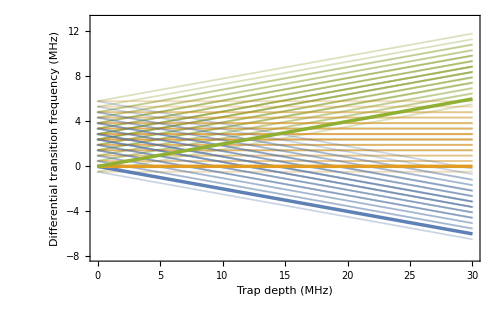

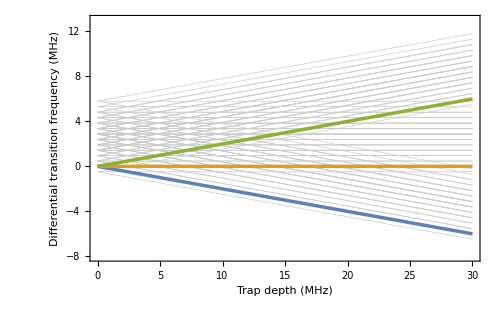

```mathematica
Show[up,mid,down,lmagic,FrameLabel->{"Trap depth (MHz)","Differential transition frequency (MHz)"}]
Show[lAll,lmagic,FrameLabel->{"Trap depth (MHz)","Differential transition frequency (MHz)"}]
```